## Важные функции и символы

```mathematica
grids[dist_]:=Table[If[OddQ@Round@(i/dist),{i,Dashed},{i}],{i,Ceiling@(#1/dist)*dist,Floor@(#2/dist)*dist,dist}]&;
Needs@"ErrorBarPlots`";
dropLastDot@string_:=If[StringTake[string,-1]===".",StringDrop[string,-1],string];
vertSize=0.01;horizSize=0.03;
vertCross[coord1_,coord2_]:={Line@{coord1,coord2},Line/@({{#1+vertSize,#2},{#1-vertSize,#2}}&@@@{coord1,coord2})};
horizCross[coord1_,coord2_]:={Line@{coord1,coord2},Line/@({{#1,#2+horizSize},{#1,#2-horizSize}}&@@@{coord1,coord2})};
```

## Импорт табличных данных

```mathematica
data=Cases[Import[
"/Users/leonidbarinov/Desktop/МФТИ/Лабораторные работы/1.1.1 (Определение систематических и случайных погрешностей при измерении удельного сопротивления нихромовой проволки)/darova.xlsx"
]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
data//TableForm
data1=Cases[Import[
"/Users/leonidbarinov/Desktop/МФТИ/Лабораторные работы/1.1.1 (Определение систематических и случайных погрешностей при измерении удельного сопротивления нихромовой проволки)/darova2.xlsx"
]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
data1//TableForm
```

81.5 | 176.
108.6 | 236.
130.3 | 280.
147.3 | 320.
173.5 | 368.
204.5 | 440.
230.8 | 496.
257.8 | 532.
270.1 | 576.
280.4 | 600.
285.7 | 612.

75.2 | 236.
81.7 | 264.
94.3 | 300.
106.7 | 340.
118.4 | 376.
135.2 | 428.
142.9 | 464.
161.5 | 500.
171.7 | 540.
186.1 | 584.
191.1 | 600.

## Фитирование табличных данных линейной функцией

| Estimate | Standard Error | t-Statistic | P-Value
1 | 6.33672 | 5.83229 | 1.08649 | 0.305504
x | 2.1038 | 0.027863 | 75.5052 | 6.34272×10^-14

| Estimate | Standard Error | t-Statistic | P-Value
1 | 8.88425 | 5.95208 | 1.49263 | 0.169734
x | 3.09549 | 0.0428702 | 72.2062 | 9.47628×10^-14

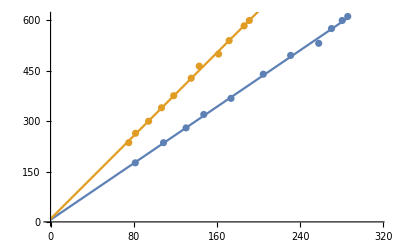

```mathematica
forFit=data;
fit=LinearModelFit[forFit,{1,x},x];
forFit1=data1;
fit1=LinearModelFit[forFit1,{1,x},x];
fit@"ParameterTable"
fit1@"ParameterTable"
Show[
ListPlot[{forFit,forFit1},PlotRange->{{0,1.1Max@@Join[forFit⟦All,1⟧,forFit1⟦All,1⟧]},Automatic}],
Plot[{fit@x,fit1@x},{x,0,Max@@Join[forFit⟦All,1⟧,forFit1⟦All,1⟧]}]
]
```

## универс

```mathematica
files={
"/Users/leonidbarinov/Desktop/МФТИ/Лабораторные работы/1.1.1 (Определение систематических и случайных погрешностей при измерении удельного сопротивления нихромовой проволки)/darova.xlsx",
"/Users/leonidbarinov/Desktop/МФТИ/Лабораторные работы/1.1.1 (Определение систематических и случайных погрешностей при измерении удельного сопротивления нихромовой проволки)/darova2.xlsx",
"/Users/leonidbarinov/Desktop/МФТИ/Лабораторные работы/1.1.1 (Определение систематических и случайных погрешностей при измерении удельного сопротивления нихромовой проволки)/darova3.xlsx"
};
```

```mathematica
data=Cases[Import[#]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]]&/@files;
```

## Фитирование табличных данных линейной функцией

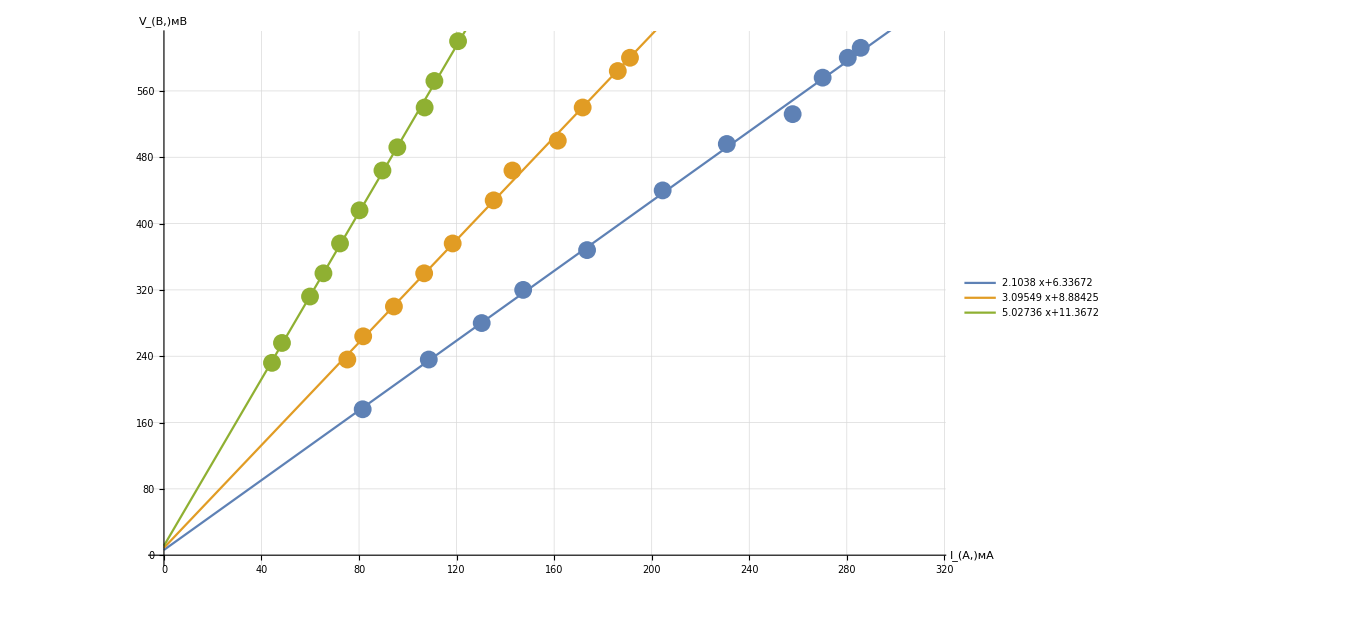

```mathematica
forFit=data⟦All,All,;;2⟧;
fit=LinearModelFit[#,{1,x},x]&/@forFit;

rangecoef=1.1;
Show[
ErrorListPlot[
Apply[{{#1,#2},ErrorBar@#3}&,data,{2}],
PlotRange->{{0,rangecoef Max@@Join@@data⟦All,All,1⟧},Automatic},
ImageSize->1000,
GridLines->{grids@20,grids@20},
AxesLabel->(Style[#,Bold,Black, Large]&)/@{"I_(A,)мА","V_(B,)мВ"}
],
Plot[
Evaluate@Through@fit@x,
{x,0,rangecoef Max@@Join@@data⟦All,All,1⟧},
PlotLegends->Through@fit@"BestFit"]
]
Export["/Users/leonidbarinov/Desktop/МФТИ/Лабораторные работы/1.1.1 (Определение систематических и случайных погрешностей при измерении удельного сопротивления нихромовой проволки)/15.png",%];
```

## Создание своих ticks для графика

```mathematica
myTicX[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,0.5}]
```

```mathematica
myTicY[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,5}]
```

## Экспорт в Latex

```mathematica
forTeX=MapAt[dropLastDot@*ToString,data,{{2;;,All}}];
forTeX//TeXForm
```

\left(
\begin{array}{ccccccccccc}
 \{81.5,176.,1.2\} & \{108.6,236.,1.2\} & \{130.3,280.,1.2\} & \{147.3,320.,1.2\} & \{173.5,368.,1.2\} & \{204.5,440.,1.2\} & \{230.8,496.,1.2\} & \{257.8,532.,1.2\} & \{270.1,576.,1.2\} &
   \{280.4,600.,1.2\} & \{285.7,612.,1.2\} \\
 \text{$\{$75.2, 236., 1.2$\}$} & \text{$\{$81.7, 264., 1.2$\}$} & \text{$\{$94.3, 300., 1.2$\}$} & \text{$\{$106.7, 340., 1.2$\}$} & \text{$\{$118.4, 376., 1.2$\}$} & \text{$\{$135.2, 428., 1.2$\}$}
   & \text{$\{$142.9, 464., 1.2$\}$} & \text{$\{$161.5, 500., 1.2$\}$} & \text{$\{$171.7, 540., 1.2$\}$} & \text{$\{$186.1, 584., 1.2$\}$} & \text{$\{$191.1, 600., 1.2$\}$} \\
 \text{$\{$44.3, 232., 1.2$\}$} & \text{$\{$48.4, 256., 1.2$\}$} & \text{$\{$59.9, 312., 1.2$\}$} & \text{$\{$65.4, 340., 1.2$\}$} & \text{$\{$72.2, 376., 1.2$\}$} & \text{$\{$80.2, 416., 1.2$\}$} &
   \text{$\{$89.6, 464., 1.2$\}$} & \text{$\{$95.7, 492., 1.2$\}$} & \text{$\{$106.9, 540., 1.2$\}$} & \text{$\{$110.9, 572., 1.2$\}$} & \text{$\{$120.6, 620., 1.2$\}$} \\
\end{array}
\right)